# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order2_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles[[1]]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse2\1) Fitting Scale\Export

# Parametrization of the Lobe’s Flattening Factor σ_n

```mathematica
paramsFlat = Table[Table[rawFiles[[albedo]][[j]][[i]][[4]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsFlat[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsFlat[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsFlat[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Green],
ListPlot3D[paramsFlat[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Yellow]
 ]
```

-Graphics3D-

We see that for most albedo values, the shape is very similar and there is no dependency on the albedo at all, which is good (only the global scale factor σ should be dependent on albed).
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in α is from index 1 to about 9.
There is also a slight inflection of the curve for grazing angles indicating a slight dependency on θ.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

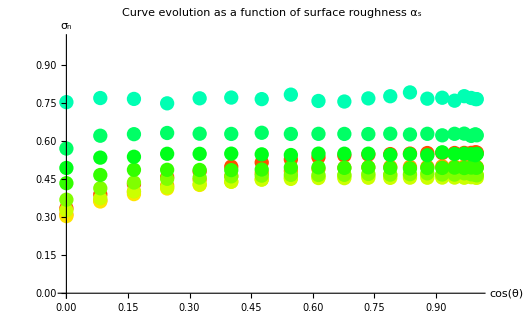

```mathematica
paramsFlat0=paramsFlat[[1]]; (* We only work on albedo = 1 *)
parmsFlatCurves= Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,9}];
Show[Table[ListPlot[parmsFlatCurves[[j]],PlotRange->{0,1},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ_n"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,9}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0.339329 | b→0.622697 | c→-0.626894 | d→0.220323
a→0.31593 | b→0.592298 | c→-0.651705 | d→0.243475
a→0.311579 | b→0.566671 | c→-0.715804 | d→0.307063
a→0.333094 | b→0.48649 | c→-0.645465 | d→0.28366
a→0.377026 | b→0.421443 | c→-0.62222 | d→0.294613
a→0.442426 | b→0.261177 | c→-0.414505 | d→0.207998
a→0.503848 | b→0.27316 | c→-0.473116 | d→0.247237
a→0.584873 | b→0.294019 | c→-0.525746 | d→0.274938
a→0.759907 | b→0.00825768 | c→0.038203 | d→-0.0373624)

Now let’s try and fit the individual parameters using another fitting for each one:

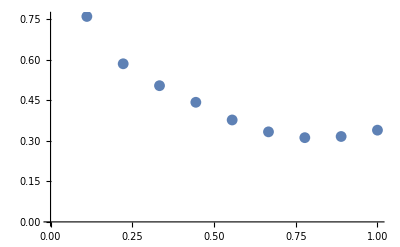

```mathematica
paramsFlatA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatA]
ListPlot[paramsFlatB];
ListPlot[paramsFlatC];
ListPlot[paramsFlatD];
```

Parameter A is the most stable so let’s start with that one...

0.913643-1.65548 α+1.39617 α^2-0.320331 α^3

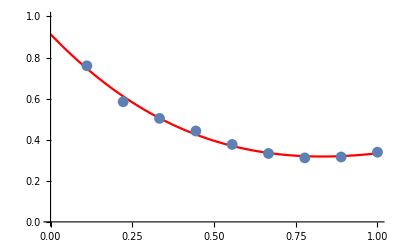

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsFlatA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1}],
ListPlot[paramsFlatA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0.658829 | c→-0.693329 | d→0.256351
a→0. | b→0.562876 | c→-0.597607 | d→0.214138
a→0. | b→0.510106 | c→-0.611801 | d→0.250662
a→0. | b→0.469538 | c→-0.614295 | d→0.266756
a→0. | b→0.469616 | c→-0.710793 | d→0.342646
a→0. | b→0.37567 | c→-0.625017 | d→0.322159
a→0. | b→0.264803 | c→-0.45775 | d→0.238904
a→0. | b→0.115613 | c→-0.19772 | d→0.0970483
a→0. | b→0.0991628 | c→-0.12894 | d→0.0532796)

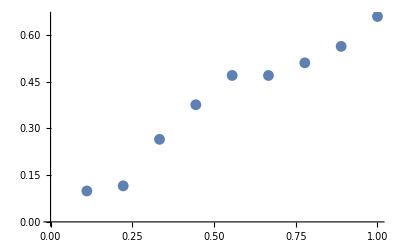

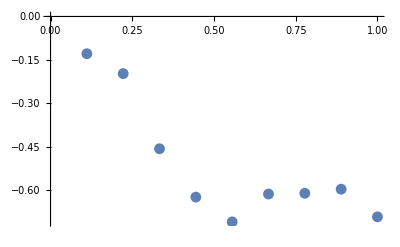

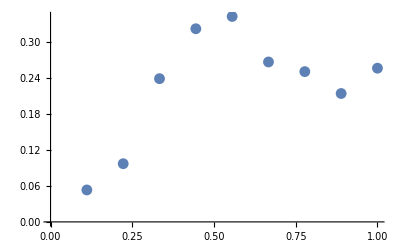

```mathematica
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatB->{0,1}]
ListPlot[paramsFlatC->{-1,0}]
ListPlot[paramsFlatD->{0,1}]
```

We see the model is behaving a little bit better now so we can proceed and fit the next coefficients:

0.0447239+0.62474 α

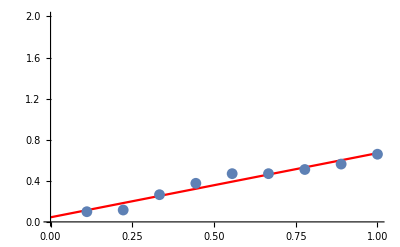

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+0*c*u^2+0*d*u^3;
fittingB = FindFit[ paramsFlatB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{0,2}],
ListPlot[paramsFlatB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→3.33067×10^-16 | c→-0.722777 | d→0.275551
a→0. | b→5.55112×10^-16 | c→-0.70054 | d→0.281253
a→0. | b→6.66134×10^-16 | c→-0.668641 | d→0.287724
a→0. | b→2.22045×10^-16 | c→-0.591254 | d→0.251733
a→0. | b→2.22045×10^-16 | c→-0.495316 | d→0.202148
a→0. | b→2.22045×10^-16 | c→-0.477469 | d→0.225953
a→0. | b→3.33067×10^-16 | c→-0.424985 | d→0.21754
a→0. | b→3.33067×10^-16 | c→-0.385859 | d→0.219721
a→0. | b→2.77556×10^-17 | c→-0.170411 | d→0.0803206)

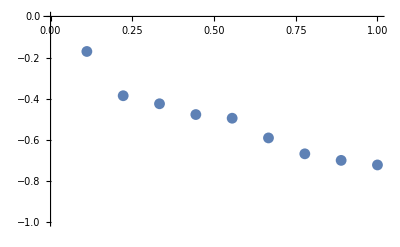

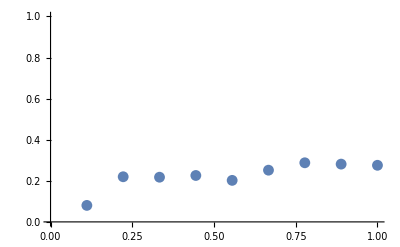

```mathematica
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatC,PlotRange->{-1,0}]
ListPlot[paramsFlatD,PlotRange->{0,1}]
```

The model is continuing to improve in stability, let’s keep on replacing...

-0.118844-0.973213 α+0.36902 α^2

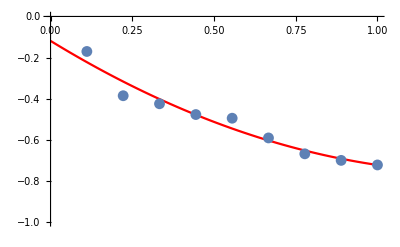

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+0*d*u^3;
fittingC = FindFit[ paramsFlatC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-1,0}],
ListPlot[paramsFlatC]
]
```

#### Replacing C and Fitting D

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→0.275832
a→0. | b→0. | c→0. | d→0.27241
a→0. | b→0. | c→0. | d→0.270351
a→0. | b→0. | c→0. | d→0.26511
a→0. | b→0. | c→0. | d→0.256467
a→0. | b→0. | c→0. | d→0.227055
a→0. | b→0. | c→0. | d→0.192987
a→0. | b→0. | c→0. | d→0.14525
a→0. | b→0. | c→0. | d→0.136481)

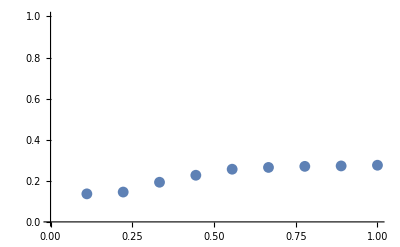

```mathematica
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatD,PlotRange->{0,1}]
```

0.132577+0.16975 α

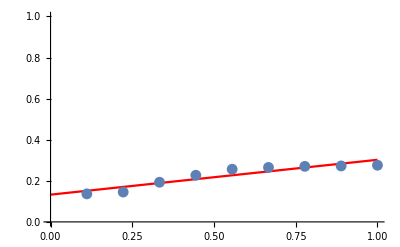

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+0*c*u^2+0*d*u^3;
fittingD = FindFit[ paramsFlatD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1}],
ListPlot[paramsFlatD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.913643-1.65548 α+1.39617 α^2-0.320331 α^3
	b(α_s)= 0.0447239+0.62474 α
	c(α_s)= -0.118844-0.973213 α+0.36902 α^2
	d(α_s)=0.132577+0.16975 α
	
	σ_n(μ,α_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ]
fA[α_]= 0.9136434030473861-1.6554846256054254 α+1.396170391613371 α^2-0.3203305249468263 α^3;
fB[α_]= 0.044723925680673265+0.6247396225423497 α;
fC[α_]= -0.11884367470512597-0.973212684779483 α+0.36902017638601514 α^2;
fD[α_]=0.13257717032932556+0.1697498085943817 α;
(*fA[α_]= 0.8846422855624879-1.405547722190124 α+0.8622861833686603 α^2;
fB[α_]= 1.3711661211982282-8.51539991518015 α+5.496099699231776 α^2;
fC[α_]= 7.753321114389069-8.10901036151992 α+5.808056815711743 α^2;
fD[α_]=-3.187108490510769-0.2936373719156488 α;*)
fFlat[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];
Plot3D[fFlat[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ_n"},PlotLabel->"Lobe flattening factor",PlotRange->{0,1}]
```

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fFlat[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

# Parametrization of the lobe’s Scale factor σ

```mathematica
paramsScale = Table[Table[rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScale[[albedo]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,resZ}]
]
```

-Graphics3D-

So it appears the scale factor σ is also quite smooth and should be fitted in the same way as the flattening factor σ_n.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

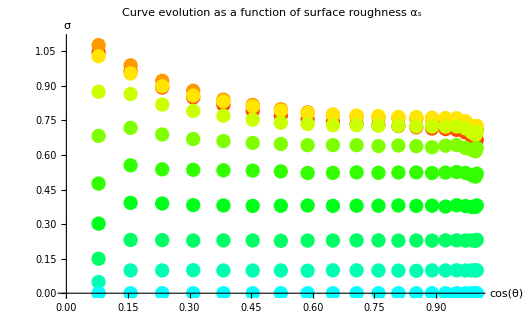

```mathematica
paramsScale0=paramsScale[[1]]; (* We only work on albedo = 1 *)
parmsScaleCurves= Table[Table[{Cos[(i-1)/resX*π/2],paramsScale0[[j]][[i]]},{i,1,resX}],{j,1,resY}];
Show[Table[ListPlot[parmsScaleCurves[[j]],PlotRange->{0,1.1},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,resY}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→1.15487 | b→-1.52259 | c→2.00818 | d→-0.963752
a→1.1874 | b→-1.55749 | c→2.06258 | d→-0.973413
a→1.12543 | b→-1.35674 | c→1.84684 | d→-0.884993
a→0.942187 | b→-0.740841 | c→0.920433 | d→-0.417535
a→0.716691 | b→-0.183988 | c→0.141715 | d→-0.0451912
a→0.477201 | b→0.369657 | c→-0.681497 | d→0.355266
a→0.293605 | b→0.53988 | c→-0.942527 | d→0.491393
a→0.135595 | b→0.553201 | c→-0.947812 | d→0.492637
a→0.0385735 | b→0.357412 | c→-0.61332 | d→0.319168
a→1.×10^-6 | b→1.83139×10^-21 | c→-4.64794×10^-21 | d→2.31341×10^-21)

Now let’s try and fit the individual parameters using another fitting for each one:

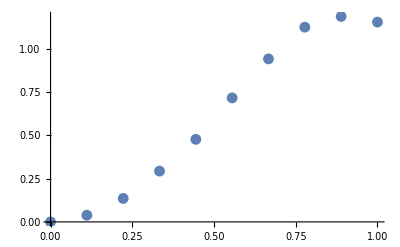

```mathematica
paramsScaleA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleA]
ListPlot[paramsScaleB];
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

All curves seem to behave the same way so let’s simply start with coefficient a:

0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3

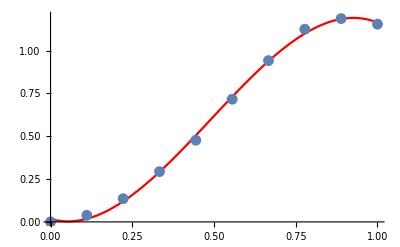

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsScaleA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1.2}],
ListPlot[paramsScaleA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-1.58908 | c→2.13055 | d→-1.03017
a→0. | b→-1.54237 | c→2.03475 | d→-0.958309
a→0. | b→-1.18495 | c→1.53063 | d→-0.713383
a→0. | b→-0.718633 | c→0.879556 | d→-0.395351
a→0. | b→-0.280394 | c→0.319165 | d→-0.141494
a→0. | b→0.17801 | c→-0.328741 | d→0.163824
a→0. | b→0.551565 | c→-0.964034 | d→0.503065
a→0. | b→0.661381 | c→-1.14694 | d→0.600702
a→0. | b→0.496211 | c→-0.868802 | d→0.457819
a→0. | b→-0.113248 | c→0.208452 | d→-0.113127)

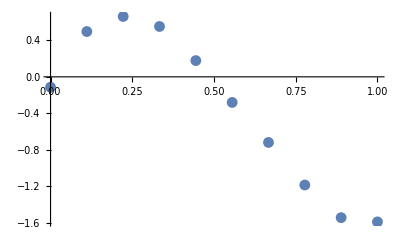

```mathematica
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleB]
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

-0.10099+7.22596 α-19.4905 α^2+10.7698 α^3

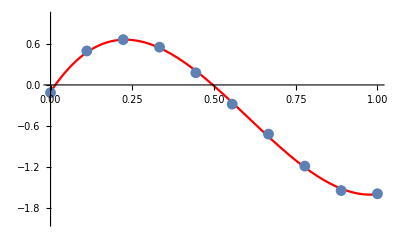

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+c*u^2+d*u^3;
fittingB = FindFit[ paramsScaleB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{-2,1}],
ListPlot[paramsScaleB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-1.77636×10^-15 | c→2.14882 | d→-1.04208
a→0. | b→-2.22045×10^-15 | c→1.95562 | d→-0.906701
a→0. | b→-1.77636×10^-15 | c→1.58353 | d→-0.747884
a→0. | b→-1.11022×10^-15 | c→0.980439 | d→-0.461145
a→0. | b→-2.22045×10^-16 | c→0.250132 | d→-0.0964717
a→0. | b→4.44089×10^-16 | c→-0.406474 | d→0.21452
a→0. | b→1.11022×10^-15 | c→-0.934598 | d→0.483868
a→0. | b→1.33227×10^-15 | c→-1.14442 | d→0.599062
a→0. | b→8.88178×10^-16 | c→-0.812948 | d→0.421392
a→0. | b→-1.66533×10^-16 | c→0.1745 | d→-0.0909845)

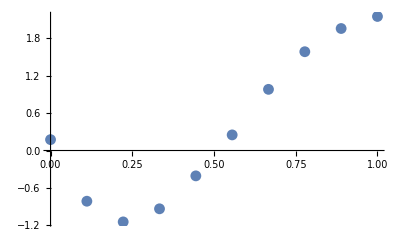

```mathematica
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleC]
ListPlot[paramsScaleD];
```

0.139826-11.4291 α+30.1773 α^2-16.7894 α^3

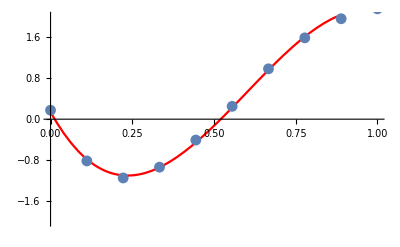

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+d*u^3;
fittingC = FindFit[ paramsScaleC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-2,2}],
ListPlot[paramsScaleC]
]
```

#### Replacing C and Fitting the D Coefficient

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→-0.987779
a→0. | b→0. | c→0. | d→-0.989869
a→0. | b→0. | c→0. | d→-0.772517
a→0. | b→0. | c→0. | d→-0.43678
a→0. | b→0. | c→0. | d→-0.0697963
a→0. | b→0. | c→0. | d→0.264574
a→0. | b→0. | c→0. | d→0.488285
a→0. | b→0. | c→0. | d→0.544596
a→0. | b→0. | c→0. | d→0.3864
a→0. | b→0. | c→0. | d→-0.0535334)

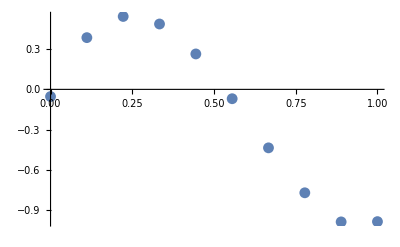

```mathematica
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleD]
```

-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3

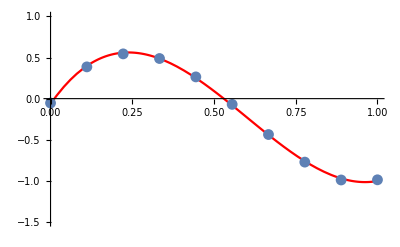

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+c*u^2+d*u^3;
fittingD = FindFit[ paramsScaleD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{-1.5,1}],
ListPlot[paramsScaleD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3
	b(α_s)= -0.10099+7.22596 α-19.4905 α^2+10.7698 α^3
	c(α_s)= 0.139826-11.4291 α+30.1773 α^2-16.7894 α^3
	d(α_s)=-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3
	
	σ(μ,σ_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ,fA,fB,fC,fD]
fA[α_]= 0.016673375075225604-0.525209545615772 α+5.24220269537287 α^2-3.5690085024568186 α^3
fB[α_]= -0.10099003574844712+7.225961805352702 α-19.49049342659228 α^2+10.769848952215131 α^3
fC[α_]= 0.13982571795990942-11.429145510606348 α+30.177292378971725 α^2-16.789426306986503 α^3
fD[α_]=-0.065024475640786+5.731247014927747 α-14.997450899818153 α^2+8.3291032822247 α^3
fScale[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];
Plot3D[fScale[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ"},PlotLabel->"Lobe Scale factor",PlotRange->{0,1.2}]
```

(0.139826-11.4291 α+30.1773 α^2-16.7894 α^3) (0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3) (-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3) (-0.10099+7.22596 α-19.4905 α^2+10.7698 α^3)

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsScale0,PlotRange->{0,1.1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fScale[Cos[(i-1)/resX π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Great!
Now we only need to find the dependence between the scale and the albedo...

# Dependence of Scale σ on albedo ρ

We try to fit our scale model to all albedo using the “amp” free coefficient to see how the amplitude is related to ρ:

```mathematica
paramsScaleMuAlpha = Table[
	Table[
		{ Cos[Mod[i,resX]/resX*π/2], 1-Quotient[i,resX]/(resY-1),paramsScale[[albedo]][[1+Quotient[i,resX]]][[1+Mod[i,resX]]]},{i,0,resX*resY-1}]
, {albedo,1,resZ}];
paramsScaleMuAlpha[[1]];
ListPlot3D[paramsScaleMuAlpha[[1]]];
```

{{amp→1.},{amp→0.766201},{amp→0.569632},{amp→0.397468},{amp→0.263022},{amp→0.22565},{amp→0.157909},{amp→0.00828737}}

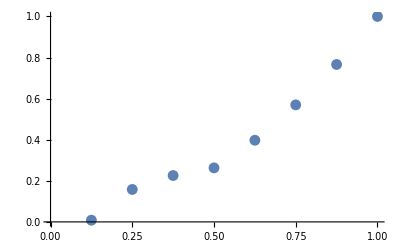

```mathematica
modelRho=amp * fScale[μ,α];
fittingRho = Table[FindFit[ paramsScaleMuAlpha[[albedo]],{modelRho},{amp},{μ,α} ],{albedo,1,resZ}]
listAmps=Table[{1-(albedo-1)/resZ, amp/.fittingRho[[albedo]]},{albedo,1,resZ}];
ListPlot[listAmps,PlotRange->{0,1}]
```

{a→0.,b→0.194911,c→0.782788}

0.194911 ρ+0.782788 ρ^2

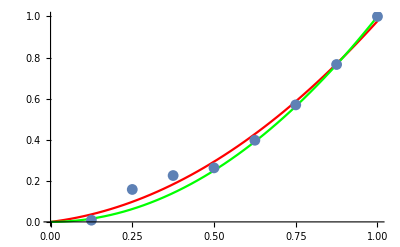

```mathematica
modelAmp=0*a+b*u+c*u^2;
fittingAmp=FindFit[listAmps,modelAmp,{a,b,c},u]
fAmp[ρ_]=Evaluate[modelAmp/.fittingAmp/.u->ρ]
fAmp2[ρ_]=ρ^2;
Show[
Plot[fAmp[ρ],{ρ,0,1},PlotStyle->Red,PlotRange->{0,1}],
Plot[fAmp2[ρ],{ρ,0,1},PlotStyle->Green,PlotRange->{0,1}],
ListPlot[listAmps]
]
```

Final Expression

We obtain the final expression for the scale parameter σ :

	a(α_s)= 0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3
	b(α_s)= -0.10099+7.22596 α-19.4905 α^2+10.7698 α^3
	c(α_s)= 0.139826-11.4291 α+30.1773 α^2-16.7894 α^3
	d(α_s)=-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3
	
	σ(μ,σ_s, ρ) = ρ^2 [ a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3]

```mathematica
fScale2[μ_,α_,ρ_] = ρ^2 * fScale[μ,α];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScaleMuAlpha[[albedo]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,6}],
Table[Plot3D[fScale2[μ,α,1-(albedo-1)/resZ],{μ,0,1},{α,0,1},{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->Red],{albedo,1,6}]
]
```

-Graphics3D-

And we’re done with a very good match for scale!